RB-SFA: Rotating Bicircular High Harmonic Generation in the Strong Field Approximation

© Emilio Pisanty, 2014

This software calculates the polarization properties of the harmonic spectra produced by multi-colour circularly polarized fields, by explicitly performing the temporal integrations of the Lewenstein model for high harmonic generation. It was used to support the calculations in the paper

    Spin conservation in bicircular high harmonic generation. E. Pisanty and M. Ivanov. arXiv:1404.6242.

It was built primarily for this setting but the code is general and it should be applicable to a wide range of SFA calculations.

The program consists of this Mathematica notebook, a PDF printout, the data used for the paper, and PDFs of the graph output. It is available under the CC-BY-SA 4.0 license. If you use this code or its results in a publication, please cite both the arXiv preprint above (or any journal publication which has superseded it) and the GitHub repository where the latest version will be available. An example citation is 

    E. Pisanty. RB-SFA: Rotating Bicircular High Harmonic Generation in the Strong Field Approximation. https://github.com/episanty/RB-SFA (2014).

To get started, run the initialization cells on this notebook. (Don’t try to run the whole notebook, which can take about 5-10 minutes recalculating the example data.) The data used in the paper is provided in gzipped format as data dump of detuning scan.txt.gz; to use it simply unzip it using your utility of choice, place it in the same directory as this notebook, and it will be ready to be imported by the code below.

This code calculates the harmonic dipole as per the original Lewenstein et al. paper,

    M. Lewenstein, Ph. Balcou, M.Yu. Ivanov, A. L’Huillier and P.B. Corkum. Theory of high-harmonic generation by low-frequency laser fields. Phys. Rev. A 49 no. 3, 2117-2132 (1994).
    
The time-dependent dipole is given by

          D(t)=ⅈ∫_0^t ⅆt'∫ⅆ^3 p d(p+A(t)) × F(t')·d(p+A(t'))×exp[-ⅈ S(p,t,t')]+c.c.

Here F(t)is the time-dependent applied electric field, with vector potential A(t); the electron charge is taken to be -1. The integration time t' can be interpreted as the ionization time and the integration limit t represents the recollision time. (Upon applying the saddle-point approximation to the temporal integrals these notions apply exactly to the corresponding quantum orbits.) The ionization and recollision events are governed by the corresponding dipole matrix elements, which are taken for a hydrogenic 1s-type orbital with characteristic momentum κ and ionization potential 1/2 κ^2:

    d(p)=p d̂ g=(8ⅈ)/π(√(2 κ^5)p)/((p^2+κ^2)^3).

(Taken from B. Podolsky & L. Pauling. Phys. Rev. 34 no. 1, 109–116 (1929).)

The action 

    S(p,t,t')=∫_t'^t ⅆt''(1/2 κ^2+1/2(p+A(t''))^2) 

is the governing factor of the integral. It is highly oscillatory and must be dealt with carefully. The momentum integral is approximated using the saddle point method; this is valid and straightforward since there is one unique saddle point,

    p(t,t')=-(∫_t'^t A(t'')ⅆt'')/(t-t').
    
After the momentum has been integrated via the saddle point method, the time-dependent dipole is given by

          D(t)=ⅈ∫_0^t ⅆt'((2π)/(ϵ+ⅈ(t-t')))^(3/2) d(p(t,t')+A(t)) × F(t')·d(p(t,t')+A(t'))×exp[-ⅈ S(p(t,t'),t,t')]+c.c.
          
A regularization factor ϵ has been introduced to prevent divergence of the prefactor as t' approaches t.

The integral is performed with respect to the excursion time τ=t-t' for simplicity. To reduce integration time, a gating function gate[ω τ] has been introduced, and the integration time has been cut short to a controllable length. This is physically reasonable as the wavepacket spreading (which scales as τ^(-3/2)) makes the contributions after the gate negligible, and it also represents the fact that the contributions of trajectories with longer excursion times are much harder to phase match, as their harmonic phase is very sensitively dependent on ionization.

The field and the vector potential.

As explained in the preprint, this is essentially a superposition of two elliptical fields: a fundamental at frequency ω1, with ellipticity controlled by a waveplate angle α, and its (presumably) second harmonic at frequency ω2, with ellipticity controlled by waveplate angle β. The elliptical fundamental is split into a superposition of right- and left-circular fields and the counter-rotating field (left-circular) is detuned by a fractional detuning δ, to a frequency (1+δ)ω1. The amplitudes of both fields are in principle equal, but they can be independently controlled. 

There are also two important phases, ϕ1 and ϕ2. In many cases, ϕ1 will only produce a rotation of the total field, but ϕ2 can change the shape of the field and thus affect the physics. The effect of ϕ2 on the spectrum is an avenue of future research.

```mathematica
A[t_,{ω1_,ω2_,δ_,F1_,F2_,α_,β_,ϕ1_,ϕ2_,envelope_}]:=envelope[t](F2/ω2{Cos[β]Cos[ω2 t-ϕ1],Sin[β]Sin[ω2 t-ϕ1]}+F1/(√2)(1/ω1 Cos[α-π/4]{Cos[ω1 t+ϕ1],-Sin[ω1 t+ϕ1]}+1/((1+δ)ω1)Sin[α-π/4]{Cos[(1+δ)ω1 t-ϕ1+ϕ2],+Sin[(1+δ)ω1 t -ϕ1+ϕ2]}));
F[t_,{ω1_,ω2_,δ_,F1_,F2_,α_,β_,ϕ1_,ϕ2_,envelope_}]=-D[A[t,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}],t];
```

The dipole transition matrix element.

```mathematica
dipole[{px_,py_},κ_]:=(8ⅈ)/π(√(2 κ^5){px,py})/((px^2+py^2+κ^2)^3)
```

Various field envelopes.

```mathematica
flatTopEnvelope[ω_,num_,nRamp_]:=Function[t,Piecewise[{{0,t<0},{Sin[(ω t)/(4nRamp)]^2,0≤t<(2 π)/ω nRamp},{1,(2 π)/ω nRamp≤t<(2 π)/ω(num-nRamp)},{Sin[(ω ((2 π)/ω num-t))/(4nRamp)]^2,(2 π)/ω(num-nRamp)≤t<(2 π)/ω num},{0,(2 π)/ω num≤t}}]]
flatEnvelope[ω_,num_]:=Function[t,1(*Piecewise[{{0,t<0},{1,0≤t<(2 π)/ω num},{0,(2 π)/ω num≤t}}]*)]
```

This is a visualization function which helps picture the field in different configurations

```mathematica
(*DynamicModule[
{F1=1,F2=1,ω2=2 2π,ω1=2π,α,β,n=15,envelope=1&},
Manipulate[
α=a °;β=b °;
Show[
ParametricPlot[
F[t,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}]
,{t,0,15}
,PlotRange->2
,Frame->True
,Axes->None
,ImageSize->600
,PlotPoints->100
],
Graphics[{PointSize[Large],
Point[F[tm,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}]]
}]
]
,{{tm,6,"t"},0,15,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
,{{δ,0,"ω'/ω-1"},-0.1,0.1,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
,{{a,45,"α"},-90,90,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
,{{b,45,"β"},-90,90,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
,{{ϕ1,0,"ϕ_1"},0,2π,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
,{{ϕ2,1,"ϕ_2"},0,2π,ControlType->Slider,ImageSize->600,Appearance->"Labeled"}
]
]*)
```

The standard options for the duration of the pulse and the resolution are

```mathematica
standardOptions={"npp"->90,"nTop"->10,"nRamp"->3,"num"->Automatic,"ω1"->0.057};
```

npp dictates how many sampling points are used per laser cycle (at frequency ω1, of the infrared laser), and it should be at least twice the highest harmonic of interest. For a flat top envelope, nRamp and nTop give the durations of the on- and off- ramps, and of the flat top, in laser cycles. The total duration is num=2nRamp+nTop, and can be specified independently. ω1 is the frequency of the fundamental laser, in atomic units.

harmonicOrderAxis produces a list that can be used as a harmonic order axis for the given pulse parameters. 

The length can be fine-tuned (to match exactly a spectrum, for instance, and get a matrix of the correct shape) using the correction option, or a TargetLength can be directly specified.

```mathematica
Options[harmonicOrderAxis]=standardOptions~Join~{"correction"->1,"TargetLength"->Automatic};
harmonicOrderAxis::target="Invalid TargetLength option `1`. This must be a positive integer or Automatic.";
harmonicOrderAxis[OptionsPattern[]]:=Module[
{nTop,nRamp,num,npp},
nTop=OptionValue["nTop"];
nRamp=OptionValue["nRamp"];
num=2nRamp+nTop;
npp=OptionValue["npp"];

Piecewise[{
{1/num Range[0.,Round[(npp num+1)/2.]-1+OptionValue["correction"]],OptionValue["TargetLength"]===Automatic},
{Round[(npp num+1)/2.]/num Range[0,OptionValue["TargetLength"]-1]/OptionValue["TargetLength"],IntegerQ[OptionValue["TargetLength"]]&&OptionValue["TargetLength"]≥0}
},
Message[harmonicOrderAxis::target,OptionValue["TargetLength"]];Abort[]
]
]
```

timeAxis produces a list that can be used as a time axis for the given pulse parameters.

```mathematica
Options[timeAxis]=standardOptions~Join~{"Scale"->"AtomicUnits"};
timeAxis::scale="Invalid Scale option `1`. Available values are \"AtomicUnits\" and \"LaserPeriods\"";
timeAxis[OptionsPattern[]]:=Module[{T,num},
T=(2π)/OptionValue["ω1"];
num=If[OptionValue["num"]===Automatic,OptionValue["nTop"]+2OptionValue["nRamp"],OptionValue["num"]];
Piecewise[{
{1,OptionValue["Scale"]=="AtomicUnits"},
{1/T,OptionValue["Scale"]=="LaserPeriods"}
},
Message[timeAxis::scale,OptionValue["Scale"]];Abort[]
]×Table[t
,{t,0,num(2π)/OptionValue["ω1"],num/(num×OptionValue["npp"]+1)(2π)/OptionValue["ω1"]}
]
]
```

getSpectrum takes a time-dependent dipole list and returns its Fourier transform in absolute-value-squared. It takes as options
  · pulse parameters ω1, num and npp,
  · a polarization parameter ϵ, which gives an unpolarized spectrum when given False, or polarizes along an ellipticity ϵ if that is a number (this is meant primarily to select right- and left-circularly polarized spectra using ϵ=1 and ϵ=-1 respectively),
  · a DifferentiationOrder, which can return the dipole value (default,=0), velocity (=1), or acceleration (=2), 
  · a power of ω, ωPower, with which to multiply the spectrum before returning it (which should be equivalent to DifferentiationOrder except for pathological cases), and
  · a Part function to apply immediately after differentiation (default is the identity function, but Re, Im, or Abs[#]^2& are reasonable choices).
If no option is passed to ωPower and DifferentiationOrder, the pulse parameters do not really affect the output, except by a global factor of num.

```mathematica
Options[getSpectrum]={"ϵ"->False,"Part"->(#&),"ωPower"->0,"DifferentiationOrder"->0}~Join~standardOptions;
getSpectrum::diffOrd="Invalid differentiation order `1`.";
getSpectrum::ωPow="Invalid ω power `1`.";
getSpectrum[dipoleList_,OptionsPattern[]]:=Module[
{ϵ,differentiatedList,depth,
δt=(2π/OptionValue["ω1"])/OptionValue["npp"],
num=If[NumberQ[OptionValue["num"]],OptionValue["num"],2OptionValue["nRamp"]+OptionValue["nTop"]]
},

differentiatedList=OptionValue["Part"][Piecewise[{
{dipoleList,OptionValue["DifferentiationOrder"]==0},
{1/(2δt)(Most[Most[dipoleList]]-Rest[Rest[dipoleList]]),OptionValue["DifferentiationOrder"]==1},
{1/δt^2(Most[Most[dipoleList]]-2Most[Rest[dipoleList]]+Rest[Rest[dipoleList]]),OptionValue["DifferentiationOrder"]==2}},
Message[getSpectrum::diffOrd,OptionValue["DifferentiationOrder"]];Abort[]
]];

If[NumberQ[OptionValue["ωPower"]],Null;,Message[getSpectrum::ωPow,OptionValue["ωPower"]];Abort[]  ];

num Table[
(OptionValue["ω1"]/num k)^(2OptionValue["ωPower"]),{k,1,Round[Length[differentiatedList]/2]}
]×If[NumberQ[ϵ=OptionValue["ϵ"]],
(*polarized spectrum*)
Abs[
Transpose[Table[
Fourier[
Re[differentiatedList⟦All,i⟧]
,FourierParameters->{-1, 1}
]
,{i,1,2}]]⟦1;;Round[Length[differentiatedList]/2]⟧.({1,ⅈ ϵ}/(√(1+Abs[ϵ]^2)))
]^2
,
(*unpolarized spectrum*)
depth=If[Length[#]>1,#⟦2⟧,#⟦1⟧]&[Dimensions[dipoleList]];
Sum[Abs[
Fourier[
If[depth>1,Re[differentiatedList⟦All,i⟧],Re[differentiatedList⟦i⟧]]
(*funky depth thing so this can take lists of numbers and lists of vectors, of arbitrary length. Makes for easier benchmarking.*)
,FourierParameters->{-1, 1}
]⟦1;;Round[Length[differentiatedList]/2]⟧
]^2,{i,1,depth}]
]
]
```

The following can be used to benchmark this code

```mathematica
(*Module[{npp=5000,num=4,ω=2},
ListLinePlot[
Transpose[{harmonicOrderAxis["correction"->0,"npp"->npp,"nRamp"->0,"nTop"->num(*,"ω1"->ω*)],
getSpectrum[ 
Table[
{1,0}Sin[ω t]+{0,1}Sin[2 ω t]+{0,1}Sin[3 ω t]
,{t,0,num (2π)/ω,1/npp(2π)/ω}]
,"DifferentiationOrder"->0,"ωPower"->0,"ω1"->ω,"num"->num,"npp"->npp]
}]
,PlotRange->{{0,4},Full}
,ImageSize->400
,Frame->True
]
]*)
```

spectrumPlotter takes a spectrum and a list of options and returns a plot of the spectrum. The available options are
  · an Axis option, which will give the harmonic order as a horizontal axis by default, and an arbitrary scale with any other option,
  · all the options of harmonicOrderAxis, which will be passed to the call that makes the horizontal axis, and
  · all the options of ListLinePlot, which will be used to format the plot.

```mathematica
Options[spectrumPlotter]=Join[{"Axis"->"HarmonicOrder"},Options[harmonicOrderAxis],Options[ListLinePlot]];
spectrumPlotter[spectrum_,options:OptionsPattern[]]:=ListPlot[
{If[OptionValue["Axis"]==="HarmonicOrder",
harmonicOrderAxis["TargetLength"->Length[spectrum],Sequence@@FilterRules[{options}~Join~Options[spectrumPlotter],Options[harmonicOrderAxis]]],
Range[Length[spectrum]]
],
Log[10,spectrum]
}ᵀ
,Sequence@@FilterRules[{options},Options[ListLinePlot]]
,Joined->True
,PlotRange->Full
,PlotStyle->Thick
,Frame->True
,Axes->False
,ImageSize->800
]
```

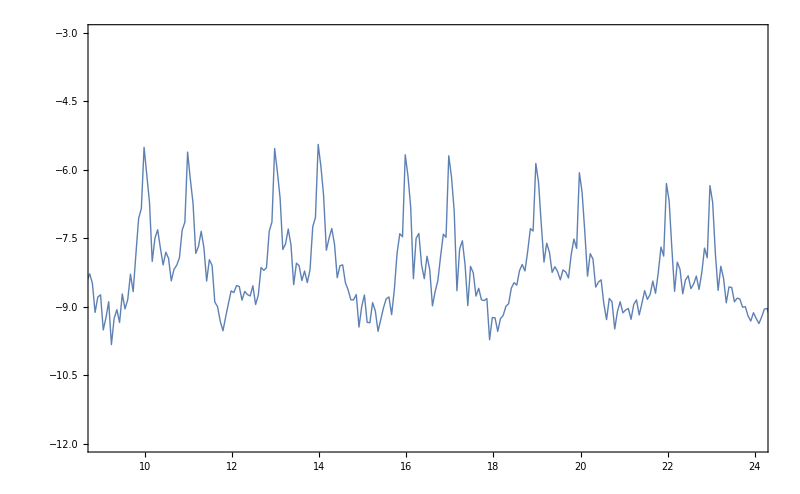

```mathematica
spectrumPlotter[getSpectrum[testDipoleList],PlotRange->{{9,24},{-12,-3}}]
```

biColorSpectrum takes a time-dependent dipole list and produces overlaid plots of the right- and left-circular components of the spectrum, in red and blue respectively. It takes all the options of getSpectrum and spectrumPlotter, which are passed directly to the corresponding calls, as well as the options of Show, which can be used to modify the plot appearance.

```mathematica
Options[biColorSpectrum]=Join[{PlotRange->All},Options[Show],Options[spectrumPlotter],DeleteCases[Options[getSpectrum],"ϵ"->False]];
biColorSpectrum[dipoleList_,options:OptionsPattern[]]:=Show[{
spectrumPlotter[
getSpectrum[dipoleList,"ϵ"->1,Sequence@@FilterRules[{options},Options[getSpectrum]]],
PlotStyle->Red,Sequence@@FilterRules[{options},Options[spectrumPlotter]]],
spectrumPlotter[
getSpectrum[dipoleList,"ϵ"->-1,Sequence@@FilterRules[{options},Options[getSpectrum]]],
PlotStyle->Blue,Sequence@@FilterRules[{options},Options[spectrumPlotter]]]
}
,PlotRange->OptionValue[PlotRange]
,Sequence@@FilterRules[{options},Options[Show]]
]
```

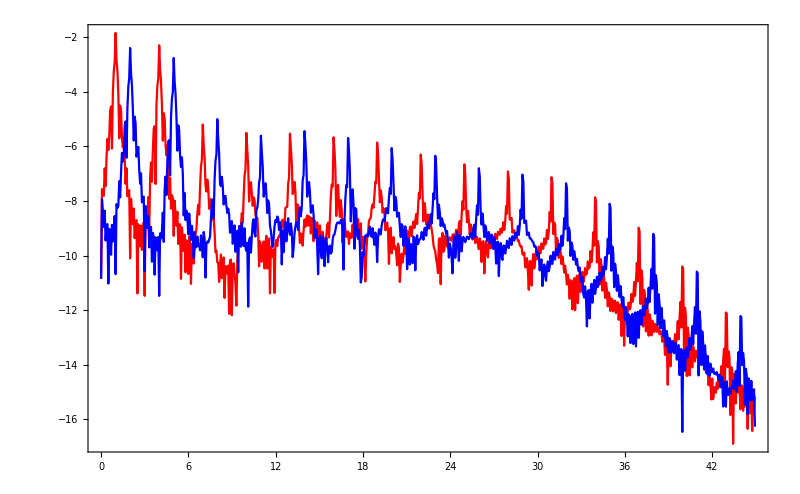

```mathematica
biColorSpectrum[testDipoleList]
```

The functions below can be used for rudimentary Gabor analysis of the signal. This is useful to check for certain artifacts (for example, if the ramps are too steep then the spectrum can get distorted by large contributions coming from the topmost periods of the on- and off-ramps.

gaussianGate takes a central time t0 and a width σ and returns a gaussian gate (i.e. a list with a gaussian profile around that central time) which should multiply the time series to be analysed. Both arguments can be functions of the strings "T" and "ω1", which will be substituted for a single cycle of the laser fundamental and its frequency, respectively.

```mathematica
Options[gaussianGate]=standardOptions;
gaussianGate[t0_,σ_]:=gaussianGate[t0,σ,Sequence@@Options[gaussianGate]]
gaussianGate[t0_,σ_,options:OptionsPattern[]]:=Table[
Exp[-1/2(t-t0)^2/σ^2]/.{"ω1"->OptionValue["ω1"],"T"->2π/OptionValue["ω1"]}
,{t,timeAxis[options]}
]
```

getGaborSpectrum takes a time-dependent dipole list, and returns the corresponding Gabor spectrogram data. Note that for long pulses and high resolutions (large npp) this can be quite expensive to compute.

The data is returned in a format that is amenable to Interpolation: that is, a list of entries of the form {{t,ω/ω1},f(t,ω)}, where t is the time coordinate on the spectrogram, ω/ω1 is the harmonic order coordinate, and f(t,ω) is the signal density at that time-frequency pair.

This takes the standard pulse options and those of timeAxis and getSpectrum, which are passed to the respective calls.

```mathematica
Options[getGaborSpectrum]=Join[standardOptions,Options[timeAxis],Options[getSpectrum]];
getGaborSpectrum[dipoleList_,σ_,options:OptionsPattern[]]:=Flatten[Table[
Function[spectrum,
{
{t,#}&/@harmonicOrderAxis["TargetLength"->Length[spectrum],Sequence@@FilterRules[{options},Options[harmonicOrderAxis]]],
spectrum
}ᵀ
][getSpectrum[
dipoleList×gaussianGate[t,σ,Sequence@@FilterRules[{options},Options[gaussianGate]]]
,Sequence@@FilterRules[{options},Options[getSpectrum]]
]]
,{t,timeAxis[Sequence@@FilterRules[{options},Options[timeAxis]]]}
],1]
```

getGaborInterpolation performs a Gabor analysis and returns an interpolated function which is easier to handle. The options and input are the same as for getGaborSpectrum, with the addition of the options for Interpolation (i.e. InterpolationOrder, Method, and PeriodicInterpolation). The output is a pure function of time and harmonic order, and should be used as e.g. output=getGaborInterpolation[...];    output[t,ω/ω1].

```mathematica
Options[getGaborInterpolation]=Options[getGaborSpectrum]~Join~Options[Interpolation];
getGaborInterpolation[dipoleList_,σ_,options:OptionsPattern[]]:=Interpolation[getGaborSpectrum[dipoleList,σ,options],Sequence@@FilterRules[{options},Options[Interpolation]]]
```

Sample usage:

```mathematica
(*AbsoluteTiming[testDipoleList=makeDipoleList[];](*{96.415463,Null}*)
AbsoluteTiming[interpolation=getGaborInterpolation[testDipoleList,0.05"T","nTop"->10,"nRamp"->3,"ω1"->0.057,"npp"->90];](*{394.716061,Null}*)
DensityPlot[
interpolation[t,HO]
(*,{t,First[timeAxis[]],Last[timeAxis[]]}*)
,{t,(5+1/6)(2π)/0.057,(5+1/6+2/3)(2π)/0.057}
,{HO,11.5,30}
,PlotRange->Full
,PlotPoints->500
,PlotRangePadding->0
,PlotLegends->Automatic
,ImageSize->550
,ColorFunction->ColorData["Jet"]
]*)
```

makeDipoleList is the main numerical integration function.

It can be called directly (i.e. simply makeDipoleList[]), which will use the default options. Any change can be indicated directly as needed - so, for instance, for a linearly polarized pulse, the call is makeDipoleList["α"→0°,"F2"→0] and whatever other options one requires.

The available options are:
  · the standard pulse options
  · nGate and nGateRamp, which control the length of the excursion time gate and its off-ramp
  · Gate, which controls the shape of the excursion time gate off-ramp
  · Envelope, which can be FlatTop or Flat
  · ϵCorrection, which controls the regularization correction ϵ, in atomic units
  · ω2, set by default to a perfect second harmonic
  · δ, set by default to zero
  · F1 and F2, in atomic units, set by default to equal intensities of 2×10^14 W/cm^2
  · κ, the ground state characteristic momentum in atomic units, set by default to 1.07 (i.e. I_p=0.57a.u.=15.57 eV, for argon)
  · the waveplate angles α and β, set by default to 45° (i.e. circular polarization)
  · the phases ϕ1 and ϕ2, set by default to zero.
  · Test can be set to True to check that the output does not contain Indeterminate or other non-numeric output

```mathematica
Options[makeDipoleList]=standardOptions~Join~{
"nGate"->1,"nGateRamp"->1/2,"ϵCorrection"->0.1,
"Gate"->"SineSquared","Envelope"->"FlatTop","Test"->False,
"ω2"->0.114,"δ"->0,"F1"->0.075,"F2"->0.075,"κ"->1.07,"ϕ1"->0,"ϕ2"->0,"α"->45°,"β"->45°
};
makeDipoleList::env="Wrong Envelope option `1`. Valid options are FlatTop and Flat.";
makeDipoleList::gate="Wrong Gate option `1`. Valid options are Linear and SineSquared.";
makeDipoleList[OptionsPattern[]]:=Module[{
nTop,nRamp,num,nGate,nGateRamp,
ω1,ω2,δ,F1,F2,κ,ϕ1,ϕ2,α,β,ϵ,envelope,
tol,gridPointQ,tInit,tFinal,npp,δt,
AInt,A2Int,AIntList,A2IntList,S,ps,gate,
dipoleList
},
nGate=OptionValue["nGate"];
nGateRamp=OptionValue["nGateRamp"];
nTop=OptionValue["nTop"];
nRamp=If[OptionValue["Envelope"]=="Flat",0,OptionValue["nRamp"]];
num=If[NumberQ[OptionValue["num"]],
OptionValue["num"],
If[OptionValue["Envelope"]=="Flat",nTop,nTop+2nRamp]
];
ω1=OptionValue["ω1"];
ω2=OptionValue["ω2"];
δ=OptionValue["δ"];
F1=OptionValue["F1"];
F2=OptionValue["F2"];
κ=OptionValue["κ"];
ϕ1=OptionValue["ϕ1"];
ϕ2=OptionValue["ϕ2"];
α=OptionValue["α"];
β=OptionValue["β"];
ϵ=OptionValue["ϵCorrection"];(*To avoid conflict with spectrum polarization/ellipticity.*)
Piecewise[{
{envelope=flatTopEnvelope[ω1,num,nRamp]
,OptionValue["Envelope"]=="FlatTop"},
{envelope=flatEnvelope[ω1,num];nRamp=0;num=nTop
,OptionValue["Envelope"]=="Flat"}
},Message[makeDipoleList::env,OptionValue["Envelope"]];Abort[]
];

tInit=0;
tFinal=(2π)/ω1 num;
npp=OptionValue["npp"];(*no. of integration points per laser period. Should be at least twice the highest harmonic of interest.*)

δt=(tFinal-tInit)/(num×npp+1);(*integration and looping timestep*)

tol=10^-5;
gridPointQ[t_]:=gridPointQ[t]=Abs[(t-tInit)/δt-Round[(t-tInit)/δt]]<tol&&tInit-tol≤t≤tFinal+tol;
(*Checks whether the given time is part of the time grid in use.*)

(*Gates are a function of the frequency-time product ω1 t.*)
Piecewise[{
{gate[ωτ_]:=Piecewise[{{1,ωτ≤2π nGate},{Sin[(2π(nGate+nGateRamp)-ωτ)/(4nGateRamp)]^2,2π nGate<ωτ≤2π(nGate+nGateRamp)},{0,nGate+nGateRamp<ωτ}}],OptionValue["Gate"]=="SineSquared"},
{gate[ωτ_]:=Piecewise[{{1,ωτ≤2π nGate},{-(ωτ-2π (nGate+nGateRamp))/(2π nGateRamp),nGate<ωτ≤2π (nGate+nGateRamp)},{0,2π (nGate+nGateRamp)<ωτ}}],OptionValue["Gate"]=="Linear"}}
,Message[makeDipoleList::gate,OptionValue["Gate"]];Abort[]];

(*This does an initial numerical integration of the integrals of the vector potential and its square that make up the action.*)
AIntList=δt×Accumulate[
Table[
A[t,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}]
,{t,tInit,tFinal,δt}
]
];
A2IntList=δt×Accumulate[
Table[
Norm[A[t,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}]]^2
,{t,tInit,tFinal,δt}
]
];

(*Recombination time first, then ionization time*)
AInt[t_?gridPointQ,tt_?gridPointQ]:=AInt[t,tt]=AIntList⟦Round[t/δt+1]⟧-AIntList⟦Round[tt/δt+1]⟧;
A2Int[t_?gridPointQ,tt_?gridPointQ]:=A2Int[t,tt]=A2IntList⟦Round[t/δt+1]⟧-A2IntList⟦Round[tt/δt+1]⟧;

(*Stationary momentum and action*)
ps[t_?gridPointQ,tt_?gridPointQ]:=ps[t,tt]=-1/(t-tt-ⅈ ϵ)AInt[t,tt];
S[t_?gridPointQ,tt_?gridPointQ]:=S[t,tt]=1/2(Norm[ps[t,tt]]^2+κ^2)(t-tt)+ps[t,tt].AInt[t,tt]+1/2 A2Int[t,tt];

(*Numerical integration loop*)
(dipoleList=Table[
δt Sum[(
ⅈ((2π)/(ϵ+ⅈ τ))^(3/2)dipole[ps[t,t-τ]+A[t,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}],κ]*×dipole[ps[t,t-τ]+A[t-τ,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}],κ].F[t-τ,{ω1,ω2,δ,F1,F2,α,β,ϕ1,ϕ2,envelope}]Exp[-ⅈ S[t,t-τ]]gate[ω1 τ] (*/.{Indeterminate->0}*)
),{τ,0,Min[t-tInit,(nGate+nGateRamp)(2π)/ω1],δt}]
,{t,tInit,tFinal,δt}]);
If[TrueQ[OptionValue["Test"]],Print[Tally[dipoleList/.{_?NumberQ->"✓"}]]];
dipoleList
]
```

Simplest example usage:

```mathematica
AbsoluteTiming[
testDipoleList=makeDipoleList[];
]
```

{95.865556,Null}

```mathematica
biColorSpectrum[testDipoleList]
```

-Graphics-

Some benchmarking

Linear polarization.

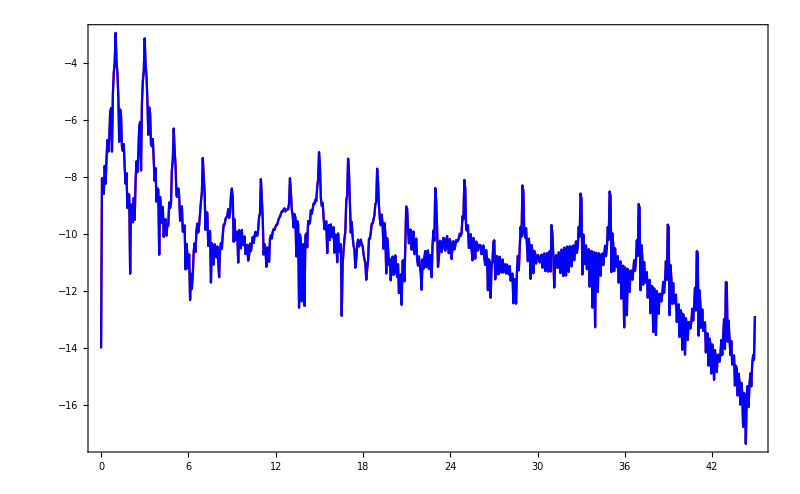
71.81472
-Graphics-

```mathematica
Column@AbsoluteTiming@biColorSpectrum[
linearDipoleList=makeDipoleList["α"->0,"F2"->0]
]
```

Using a pure sin^2 envelope, which has broader harmonics near the cutoff because less cycles contribute to those energies. The results match those obtained in the full MCTDH calculations.

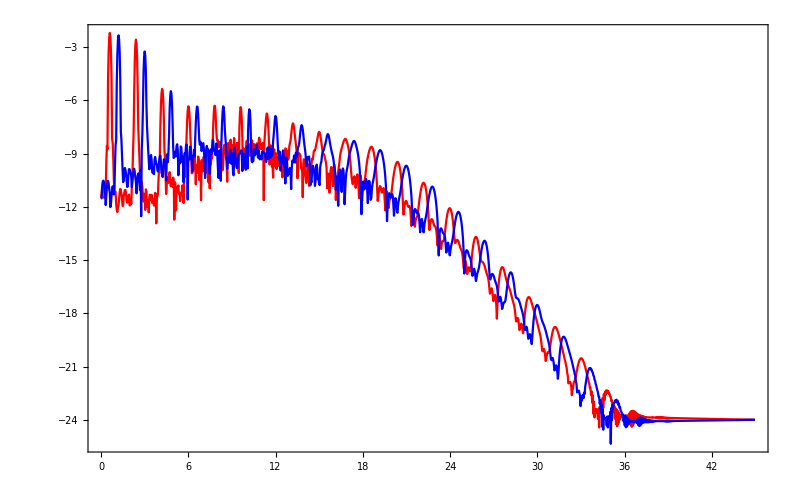
252.32682
-Graphics-

```mathematica
Column@AbsoluteTiming@biColorSpectrum[
sineSquaredDipoleList=makeDipoleList["npp"->150,"nRamp"->15/2,"nTop"->0]
]
```

Detuning scan

Log of the computation and sundry details. Expand this cell to see the code details.

Calculations were run using npp=115, nRamp=2.5 and nTop=20, with the fundamental’s ellipticity atα=35°. Detunings δ from 0 through 0.25 were calculated in steps of 0.001.

```mathematica
Quit[]
```

This is the code used to run the integrations in the paper. Runtime was about 4-5 hours on a desktop machine with an 8-thread Intel Core i7 processor at 3.4 GHz, running 8 kernels in parallel. It is quite memory-intensive, but kernels are revived automatically if they run out of memory. Each subkernel gets assigned a detuning δ, does the calculation within its own context, and then exports the result as a .mx file in a local folder.

```mathematica
directory=NotebookDirectory[];
resetMessages[symbol_]:=With[{mysymbol=symbol},
Unprotect[$MessageList];$MessageList=DeleteCases[$MessageList,HoldForm[MessageName[mysymbol,_]]];
Protect[$MessageList];]
Length[δRange=Range[0,0.25,0.001]]
```

251

```mathematica
DateString[]
NotebookSave[]
SetSharedFunction[detunedDipole];
SetSharedFunction[detuningFilename];
Print["Total = ",Length[δRange]," points at ~230s/point, will be done roughly, more or less, at about ",DateString[AbsoluteTime[]+Length[δRange]× 425. /6],"."]
ParallelTable[
Off[FrontEndObject::notavail];
detuningFilename[δ]=directory<>"data dump of detuning scan/detuning "<>ToString[δ]<>".mx";
{timing,temporaryDipoleList}=AbsoluteTiming[makeDipoleList["npp"->115,"nRamp"->2.5,"nTop"->20,"nGate"->1.3,"α"->35 °,"δ"->δ,"ω2"->1.95 0.057]];
Save[detuningFilename[δ],temporaryDipoleList];
Print["Detuning ",δ," completed at ",DateString[], " in ",timing,"s."
];
NotebookSave[];
On[FrontEndObject::notavail];
resetMessages[LaunchKernels];
detuningFilename[δ]
,{δ,δRange}
]
Beep[]
DateString[]
NotebookSave[]
```

To analyse the data, it is best to quit the kernel and reimport it.

```mathematica
Quit[]
```

These functions work with the filenames,

```mathematica
filenameToDetuning[filename_]:=ToExpression[StringDrop[Last[StringSplit[filename]],-3]]
filenameToDetuning[j_?NumberQ]:=filenameToDetuning[filenamelist⟦j⟧]
δRange=Range[0,0.25,0.001];
```

and this will Get the data back into the kernel, checking for any errors and reporting which detunings caused error messages

```mathematica
Reap[
Table[
Check[
detunedDipole[filenameToDetuning[directory<>"data dump of detuning scan/detuning "<>ToString[δ]<>".mx"]]=Get[directory<>"data dump of detuning scan/detuning "<>ToString[δ]<>".mx"];,
Sow[δ]]
,{δ,δRange}];
]⟦2⟧
```

{}

The recovered data can then be exported into a single  .mx file

```mathematica
DumpSave[NotebookDirectory[]<>"data dump of detuning scan.mx",detunedDipole]
```

{detunedDipole}

which can be read, preferably with a fresh kernel, in using

```mathematica
Quit[]
```

```mathematica
<<(NotebookDirectory[]<>"data dump of detuning scan.mx")
```

although the resulting .mx file is OS-dependent and cannot be read back in other systems (and is therefore not provided). The advantage is a smaller file (59.8MB instead of 74.7MB), and faster processing when importing.

Alternatively, the data can be exported as a Mathematica Expression to a plain-text file like the one provided.

```mathematica
Save[NotebookDirectory[]<>"data dump of detuning scan.txt",detunedDipole]
```

Again, this can be read in, with a fresh kernel, using

```mathematica
Quit[]
```

```mathematica
<<(NotebookDirectory[]<>"data dump of detuning scan.txt");
```

To analyze the data directly, simply load it in. Be sure to run the initialization cells.

```mathematica
Quit[]
```

```mathematica
AbsoluteTiming[<<(NotebookDirectory[]<>"data dump of detuning scan.txt");]
conditions:=Sequence["npp"->115,"nRamp"->2.5,"nTop"->20]
δRange=N@Range[0,25/100,1/1000];
```

{9.27863,Null}

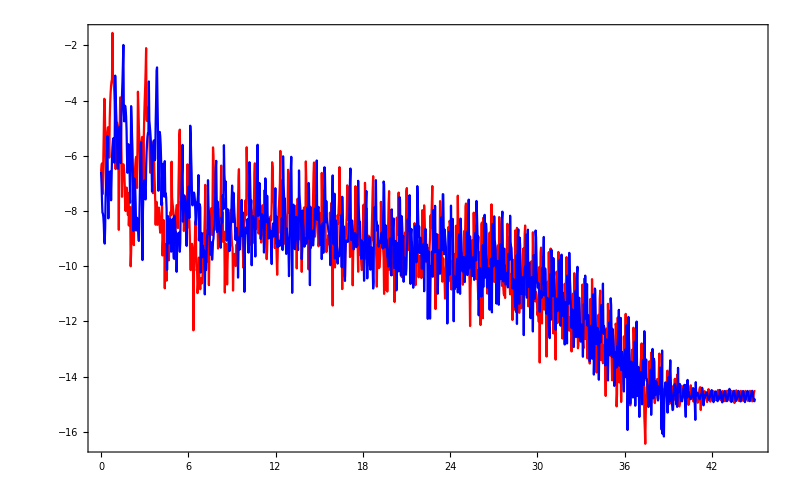

```mathematica
biColorSpectrum[detunedDipole[0.25],"Axis"->"HarmonicOrder"]
```

To simplify plotting, the interpolation step is done explicitly beforehand. This creates two pure functions, detuningInterpolation[1] and detuningInterpolation[-1], of harmonic order and detuning (i.e. the call is of the form detuningInterpolation[ϵ][ω/ω1,δ]). It is important that the interpolation be done in log scale, as otherwise artifacts appear easily.

```mathematica
Remove[detuningInterpolation]
length=Length[getSpectrum[detunedDipole[0.],"ϵ"->1]];
AbsoluteTiming[
Table[
detuningInterpolation[ϵ]=Interpolation[
Flatten[Table[
{{
harmonicOrderAxis["TargetLength"->length,conditions],
Table[δ,{length}]
}ᵀ,
Log[10,getSpectrum[detunedDipole[δ],"ϵ"->ϵ]]
}ᵀ
,{δ,δRange}],1]]
,{ϵ,{1,-1}}];
]
Remove[length];
(*(*to test:*)Plot[detuningInterpolation[1][HO,π 0.01],{HO,0,45}]*)
```

{4.84556,Null}

Some plotting niceties:

A linear scale legend up to a specified maximum and with a given ColorFunction.

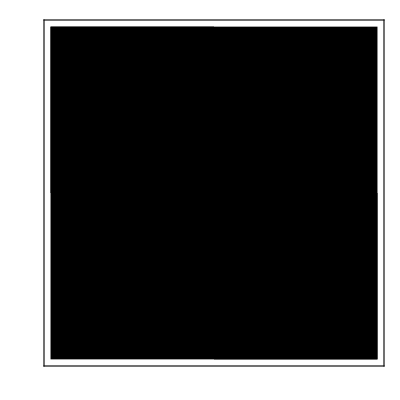
```mathematica
LinearScaleLegend[max_,colorfunction_,OptionsPattern[{"Height"->400,PlotPoints->Automatic,"Label"->None}]]:=Module[
{majorTicksList,minorTicksList},
majorTicksList=FindDivisions[{0,max(*,10^(Floor[Log[10,max]]-0)*)},5(*Round[max+1]*)];
minorTicksList=Complement[Union@@(FindDivisions[{#1,#2},5]&@@@({majorTicksList,majorTicksList⟦2⟧+majorTicksList}ᵀ)),majorTicksList];
DensityPlot[
y
,{x,0,1},{y,0,max}
,AspectRatio->20
,PlotRangePadding->0
,ImagePadding->{{1,Automatic},{Scaled[0.008],Scaled[0.008]}}
,ImageSize->{Automatic,OptionValue["Height"]}
,FrameStyle->Black
,PlotPoints->OptionValue[PlotPoints]
,ColorFunction->colorfunction
,FrameTicks->{{None,Join[
({#,N[#](*ScientificForm[N[#],1]*),{0.3,0.},{-Graphics-,AbsoluteThickness[0.25]}}&/@majorTicksList),
({#,"",{0.15,0.},{-Graphics-,AbsoluteThickness[0.125]}}&/@minorTicksList)
]},{None,None}}
,FrameLabel->{{None,OptionValue["Label"]},{None,None}}
]
]
(*(*to test:*)LinearScaleLegend[10,ColorData["WhiteJet"],"Height"->475,"Label"->"Plot Label"]*)
```

A nice colour map, which prints well on black and white.
(Taken from doi:10.1109/MAP.2002.1028735.)

```mathematica
CMRmap=Function[x,Blend[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},x]];
CMRwithMin[minIn_,minOut_:1./9]:=Function[x,CMRmap[If[x<minIn,minOut/minIn x,minOut+(1-minOut)(x-minIn)/(1-minIn)]]]
```

```mathematica
min=6. 10^-9;
max=5. 10^-7;
colorfunction=CMRwithMin[min/max];
HOTicks[ϵ_]:=({#,If[ϵ==1,Style[#,Black],""],{0.02,0},{Thickness[0.005],Gray}}&/@Range[12,18,1])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[11+1/2,18+1/4,1/4])
downTicks={{0,Style[0,Black],0},{0.25,Style[0.25,Black],0}}~Join~({#,Style[#,Black],{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
upTicks=({#,"",{0.015,0},{Thickness[0.005],Gray}}&/@Range[0.05,0.20,0.05])~Join~({#,"",{0.01,0},{Thickness[0.004],Gray}}&/@Range[0.01,0.24,0.01]);
Column@AbsoluteTiming@Row[Table[
splittingsScan[ϵ]=RegionPlot[
True
,{δ,0,0.25},{HO,11.25,18.5}
,AspectRatio->1.2
,PlotRangePadding->None
,ImagePadding->1{{35+15ϵ,20},{70,6}}
,ImageSize->{Automatic,550}
,PlotPoints->600
,FrameStyle->Automatic
,FrameLabel->{Style["ω'/ω-1",Black,12],If[ϵ==1,Style["Harmonic Order",Black,16],""]}
,ColorFunctionScaling->False
,FrameTicks->{{HOTicks[1],HOTicks[-1]},{downTicks,upTicks}}
,ColorFunction->Function[{δ,HO},colorfunction[(10^detuningInterpolation[ϵ][HO,δ])/max]]
(*,PlotLabel->Style[StringJoin[ϵ/.{1->"Right",-1->"Left"},"-circular harmonics"],Black,16]*)
]
,{ϵ,{1,-1}}]~Join~{"  ",
LinearScaleLegend[max,colorfunction,"Height"->475]
}
]
(*(*Test that it prints well in B&W:*)
Row[Table[Show[ColorConvert[%⟦1,2,1,j⟧,"Grayscale"],ImageSize->{Automatic,j/.{1->550,2->550,4->475}}],{j,{1,2,4}}]]*)
```

The image has been omitted to keep the file size small.

This makes the overlays with the channel labels. They can be made to include the actual lines predicted by uncommenting the first few lines. The exporting process changes the offsets in weird ways but they come out OK in the pdf as they are here.

```mathematica
channelLine[np_,nm_,n2_,OptionsPattern[offset->{0,0}]]:=Show[
(*Graphics[{
Thickness[0.001],Black
,Line[{{0,np+nm+1.95n2},{0.25,np+1.25nm+1.95n2}}]
}],*)
Graphics[{Text[
Style[
"("<>ToString[np]<>","<>ToString[nm]<>";"<>ToString[n2]<>")"
,14,White]
,{0.125,np+1.125nm+1.95n2+0.1},{1.35,1}OptionValue[offset],{1,0.05nm}
]}]
]
channelsList[1]={
{7,1,5,offset->{-5.75,-0.8}},
{6,-2,7,offset->{-2.5,-0.5}},
{8,5,2,offset->{5.75,-1.5}},
{7,2,4,offset->{1.0,-0.5}},
{6,-1,6,offset->{-4.75,-0.8}},
{6,0,5,offset->{-5.5,-0.8}},
{7,3,3,offset->{5.75,-0.8}},
{7,4,2,offset->{5.75,-1.}},
{5,-3,7,offset->{-2.5,-0.8}},
{6,1,4,offset->{-6.,-0.8}},
{7,5,1,offset->{5.75,-1.5}},
{5,-2,6,offset->{-2.5,-0.5}},
{6,2,3,offset->{1.0,-0.5}},
{5,-1,5,offset->{-4.75,-0.8}},
{6,3,2,offset->{5.75,-1}},
{5,0,4,offset->{-5.5,-0.8}},
{4,-3,6,offset->{-2.5,-0.8}},
{5,1,3,offset->{5.75,-0.5}},
{4,-2,5,offset->{-2.,-0.5}}};
channelsList[-1]={
{6,2,5,offset->{1.45,-0.5}},
{5,-1,7,offset->{-4.75,-0.8}},
{7,6,2,offset->{5.9,-1.6}},
{6,3,4,offset->{1.6,-0.5}},
{5,0,6,offset->{-5.5,-0.5}},
{4,-3,8,offset->{-2.,-0.8}},
{7,7,1,offset->{6.4,-1.6}},
(*{6,4,3,offset->{5.5,+1.8}},*)(*fits in the pattern but is not really visible*)
{5,1,5,offset->{1.75,-0.5}},
{4,-2,7,offset->{-2.5,-0.8}},
{5,2,4,offset->{5.5,-0.8}},
{4,-1,6,offset->{-4.75,-0.8}},
{5,3,3,offset->{1.5,-0.8}},
{4,0,5,offset->{-5.5,-0.5}},
{4,1,4,offset->{-5.5,-0.5}},
{5,4,2,offset->{5.5,-0.8}},
{4,1,4,offset->{-5.5,-0.5}},
{3,-2,6,offset->{-3.25,-0.8}},
{4,2,3,offset->{1.45,-0.5}},
{3,-1,5,offset->{-4.75,-0.8}}
};
channelsImage[ϵ_]:=Show[channelLine@@@channelsList[ϵ]
(*To see the bounding box:*)(*~Join~{Graphics[{Thickness[0.01],Line[{{0,11.25},{0.25,11.25},{0.25,18.5},{0,18.5},{0,11.25}}]}]}*)
,PlotRange->{{0,0.25},{11.25,18.5}}
,AspectRatio->1.2
,PlotRangePadding->None
,ImagePadding->None
,ImageSize->{Automatic,550}
];
Row[Table[
splittingsImage[ϵ]=Show[
{splittingsScan[ϵ],
channelsImage[ϵ]}
(*,ImageSize->750*)
]
,{ϵ,{1,-1}}]~Join~{
LinearScaleLegend[max,colorfunction,"Height"->475,PlotPoints->300]
}
]
(*(*Test that it prints well in B&W:*)
Row[Table[Show[ColorConvert[image⟦1,j⟧,"Grayscale"],ImageSize->{Automatic,j/.{1->550,2->550,3->475}}],{j,{1,2,3}}]]*)
```

The image has been omitted to keep the file size small; see instead the output pdf files provided.

This section exports the final spectra to pdf

```mathematica
res=400;
AbsoluteTiming[Export[
NotebookDirectory[]<>"/SplittingsSpectraRight.pdf"
,splittingsImage[1]
,ImageResolution->res
];]
AbsoluteTiming[Export[
NotebookDirectory[]<>"/SplittingsSpectraLeft.pdf"
,splittingsImage[-1]
,ImageResolution->res
];]
```

{3.75332,Null}

{3.54021,Null}

Nifty trick to compress the resulting pdf file (quite significantly - from ~4MB to ~380kB, per file). Uses Ghostscript to export the pdf to postscript and then back. Syntax works in a Unix system but should be easy to modify for a Windows system.

```mathematica
Run[StringJoin[
"cd "<>NotebookDirectory[]<>" && ",
"pdf2ps SplittingsSpectraRight.pdf temp.ps && ",
"ps2pdf temp.ps SplittingsSpectraRight.pdf && ",
"pdf2ps SplittingsSpectraLeft.pdf temp.ps && ",
"ps2pdf temp.ps SplittingsSpectraLeft.pdf && ",
"rm temp.ps "]]/.{0->"Success"}
```

Success

This exports the colour scale. Compression doesn’t help here

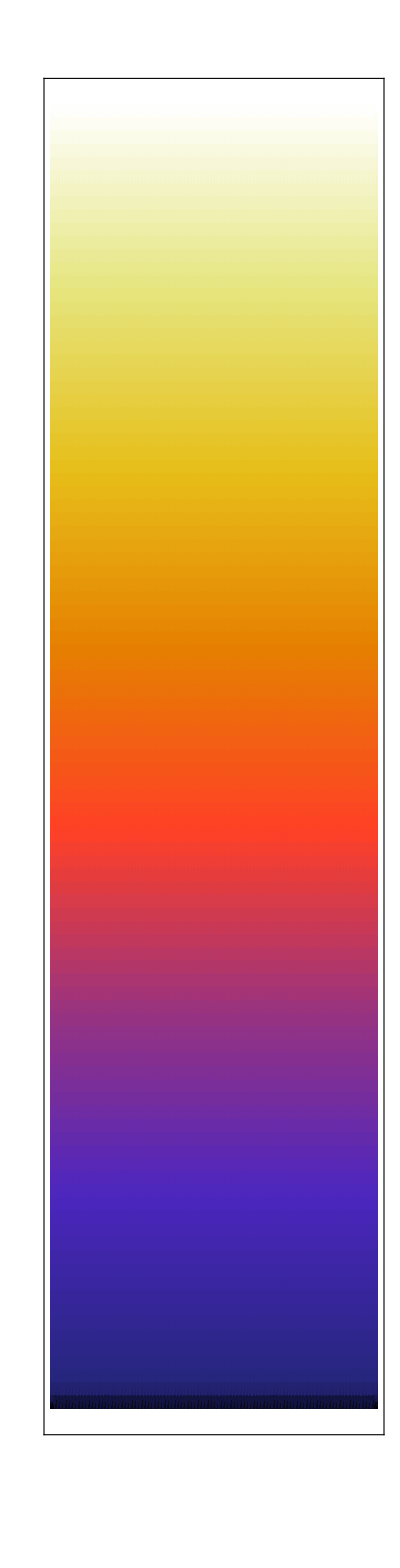

```mathematica
scale=Show[
LinearScaleLegend[10,colorfunction,"Height"->475,PlotPoints->100,"Label"->Style["Harmonic dipole (arb. units)",14]]
,ImagePadding->{{1,42},{65,4}}]
Export[
NotebookDirectory[]<>"/SplittingsSpectraColourScale.pdf"
,scale
,ImageResolution->500
];
```